# Homework 23

## Problem 23.1

In this problem, we revisit problem 22.1 but go a little further than we did before. We will work in the rest frame of the center of mass under the following conditions:
1) The particles are attracted by a central force of magnitude alpha / r^2. alpha = 0.1875*10^7
2) The masses of the two objects are m1=150 kg and m2=300 kg. 
3) The total energy is Et = -156250 J.
4) The separation distance at  t = 0 is  r0 =10 m.
5) At  t = 0, the radial velocity of each object is zero.

```mathematica
Clear["'*"];
```

First, set some numerical values.

```mathematica
m1=150;
m2=300;
r0=10;
Et=-156250;
alpha=0.1875*10^7;
```

Now we reduce the problem to a one-dimensional problem.
U0 is the original potential energy, T0 is the original kinetic energy, and p0 is the original linear momentum of the fictitious particle representing the relative motion (luckily the usual relation hold even for this fictitious particle, including the relation between kinetic energy and momentum).
L is the angular momentum.

```mathematica
M=m1+m2;
mu=m1*m2/(m1+m2);
U0=-alpha/r0;
T0=Et-U0;
p0=Sqrt[2*mu*T0];
L=p0*r0;
```

### Solutions

```mathematica
M$=m1+m2;
mu$=m1*m2/(M);
U0$=-alpha/r0;
T0$=Et-U0$;
p0$=Sqrt[2*mu*T0$];
L$=p0$*r0;
If[Abs[(M$-M)/M$]<0.01,Print["M is correct"],Print["M is incorrect."]]
If[Abs[(mu$-mu)/mu$]<0.01,Print["mu is correct"],Print["mu is incorrect."]]
If[Abs[(U0$-U0)/U0$]<0.01,Print["U0 is correct"],Print["U0 is incorrect."]]
If[Abs[(T0$-T0)/T0$]<0.01,Print["T0 is correct"],Print["T0 is incorrect."]]
If[Abs[(p0$-p0)/p0$]<0.01,Print["p0 is correct"],Print["p0 is incorrect."]]
If[Abs[(L$-L)/L$]<0.01,Print["L is correct"],Print["L is incorrect."]]
```

M is correct

mu is correct

U0 is correct

T0 is correct

p0 is correct

L is correct

As in Problem 22.1, write the radial and angular equations of motion and solve them subject the initial conditions given. Be sure to include the explicit time dependence r[t] and phi[t].
Hint: The phi equation comes from the expression for L, which is a constant of the motion.

```mathematica
req=mu*r''[t]==-alpha/r[t]^2+L^2/(mu*r[t]^3);
phieq=L==mu*phi'[t]*r[t]^2;
```

### Solutions

```mathematica
req$=mu*r''[t]==-alpha/r[t]^2+L^2/mu/r[t]^3;
phieq$=L==mu*r[t]^2*phi'[t];
If[FullSimplify[Solve[req==req$,r[t]]=={{}}],Print["req is correct."],Print["req is incorrect."]]
If[FullSimplify[Solve[phieq==phieq$,r[t]]=={{}}]Print["phieq is correct."],Print["phieq is incorrect."]];
```

req is correct.

phieq is correct.

Solve the equations and plot the orbit.

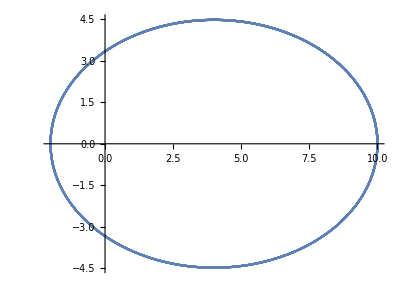

```mathematica
sol1=NDSolve[{req,phieq,r[0]==r0,r'[0]==0,phi[0]==0},{r,phi},{t,0,3}];
ParametricPlot[{r[t]*Cos[phi[t]],r[t]*Sin[phi[t]]}/.sol1,{t,0,3}]
```

In this plot, what is located at the origin?

Answer: one of the masses

### Answer

One of the masses.  Remember you are plotting the separation distance between the two objects.

Find x1(t), y1(t), x2(t), and y2(t). Plot the actual orbits of each mass.

```mathematica
x1[t]=(m2/M)*r[t]*Cos[phi[t]];
y1[t]=(m2/M)*r[t]*Sin[phi[t]];
x2[t]=-(m1/M)*r[t]*Cos[phi[t]];
y2[t]=-(m1/M)*r[t]*Sin[phi[t]];
```

### Solutions

```mathematica
x1$[t]=r[t]*Cos[phi[t]]*m2/M;
y1$[t]=r[t]*Sin[phi[t]]*m2/M;
x2$[t]=-r[t]*Cos[phi[t]]*m1/M;
y2$[t]=-r[t]*Sin[phi[t]]*m1/M;
If[FullSimplify[Solve[x1[t]==x1$[t],r[t]]=={{}}],Print["x1 is correct"],Print["x1 is incorrect"]]
If[FullSimplify[Solve[y1[t]==y1$[t],r[t]]=={{}}],Print["y1 is correct"],Print["y1 is incorrect"]]
If[FullSimplify[Solve[x2[t]==x2$[t],r[t]]=={{}}],Print["x2 is correct"],Print["x2 is incorrect"]]
If[FullSimplify[Solve[y2[t]==y2$[t],r[t]]=={{}}],Print["y2 is correct"],Print["y2 is incorrect"]]
```

x1 is correct

y1 is correct

x2 is correct

y2 is correct

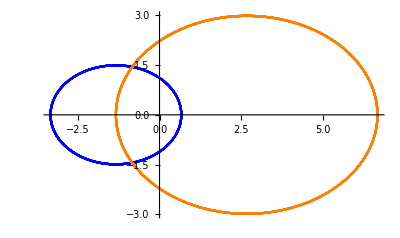

```mathematica
ParametricPlot[{{-r[t]*Cos[phi[t]]*m1/M,-r[t]*Sin[phi[t]]*m1/M}/.sol1,{r[t]*Cos[phi[t]]*m2/M,r[t]*Sin[phi[t]]*m2/M}/.sol1},{t,0,3},PlotStyle->{Blue,Orange}]
```

Now, what is at the origin?

Answer: center of mass

### Answer

The center of mass.

## Problem 23.2

For the same data as in Problem 23.1, solve the radial equation for total energies of 
-180000 J, -100000 J, -50000 J, 0 J, and + 50000 J. Plot each orbit and make a graph of the total effective potential (real + centrifugal) for each system.

```mathematica
Clear["'*"];
```

First, set the numerical values.

```mathematica
m1=150;
m2=300;
r0=10;
alpha=.1875*10^7;
```

Now we reduce the problem to a one-dimensional problem.
U0 is the original potential energy, T0 is the original kinetic energy, and p0 is the original momentum of both objects combined.
L is the angular momentum.

```mathematica
M=m1+m2;
mu=m1*m2/M;
U0=-alpha/r0;
```

We now want to plot the orbits and the energies for each of the above energies. This is most easily done using a loop. I'll provide most of the details, just fill in T0, p0, L (angular momentum), Ueff (actual plus centrifugal), and the equations for r and phi.

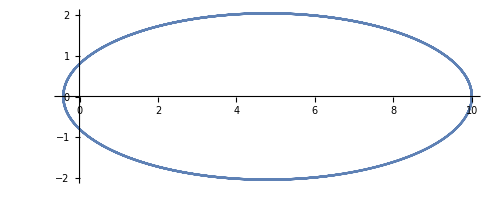
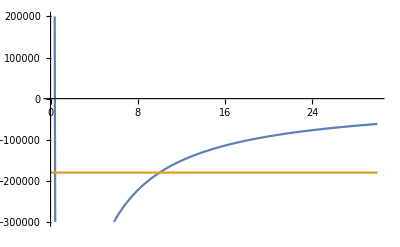
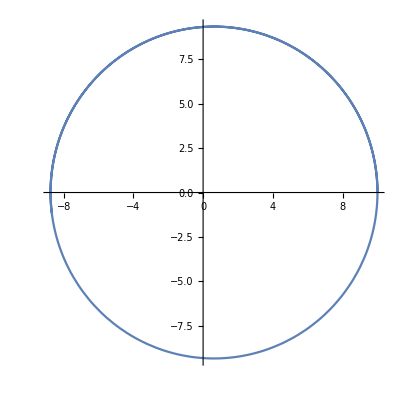
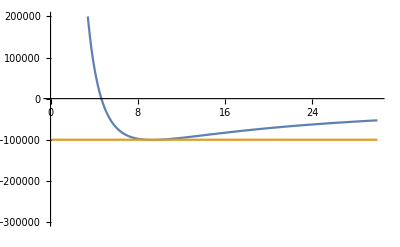
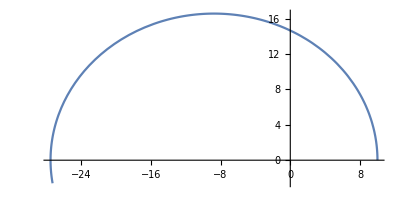
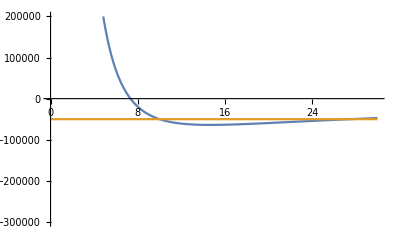
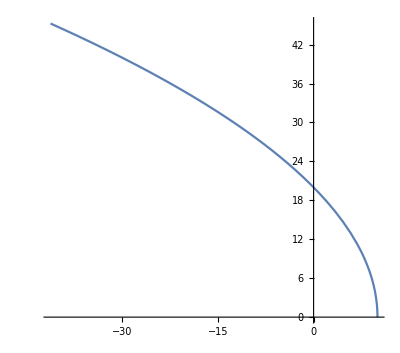
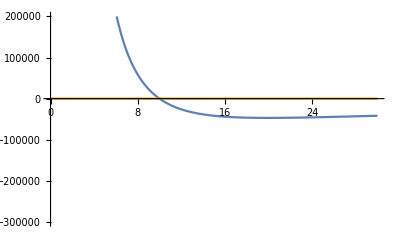

```mathematica
En={-180000,-100000,-50000,0 ,+50000};
Table[
{T0=En[[n]]-U0;
p0=Sqrt[2*mu*T0];
L=p0*r0;
Ueff=L^2/(2*mu*r^2)-alpha/r; (* use r, not r[t], for Ueff *)
req=mu*r''[t]==-alpha/r[t]^2+L^2/(mu*r[t]^3);
phieq=L==phi'[t]*(mu*r[t]^2);
sol1=NDSolve[{req,phieq,r[0]==r0,r'[0]==0,phi[0]==0},{r,phi},{t,0,2}];
ParametricPlot[{r[t]*Cos[phi[t]],r[t]*Sin[phi[t]]}/.sol1,{t,0,2}],
    Plot[{Ueff,En[[n]]},{r,0,30},PlotRange->{-3*10^5,+2*10^5}]}
,{n,1,5}
]
```

### Answers

T0=En[[n]]-U0
p0=Sqrt[2*mu*T0]
L=p0*r0
-alpha / r+L^2 / 2 / mu / r^2
req = mu*r''[ t  ]== -alpha / r[ t ]^2 + L^2 / mu / r[ t ]^3
phieq = L == mu*r[ t ]^2*phi'[ t ]

## Problem 23.3

Find the eccentricity for each orbit of Problem 23.2. Plot each orbit using Eq. 8.49 from the text combined with the initial conditions.

```mathematica
Clear["'*"];
```

```mathematica
m1=150;
m2=300;
r0=10;
alpha=.1875*10^7;
En={-180000,-100000,-50000,0,50000};
M=m1+m2;
mu=m2*m1/M;
U0=-alpha/r0;
For[i=1,i<6,i++,
  T0=En[[i]]-U0;
p0=Sqrt[2*mu*T0];
L=p0*r0;
epsilon=Sqrt[1+2*En[[i]]*L^2/alpha^2/mu];
Print[epsilon]
];
```

0.92

0.0666667

0.466667

1.

1.53333

You should now have:
   0.9200
  +0.0667
  +0.4667
  +  1.000
  +  1.533
as values of epsilon.

We'll use a different format for making the plot...

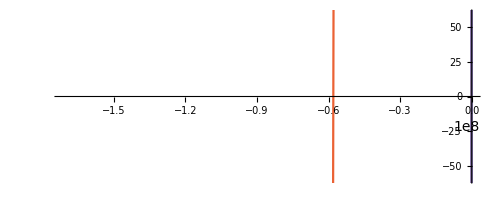

```mathematica
PolarPlot[Evaluate[{r0*(1+eps)/(1+eps*Cos[phi])}/.eps->{0.92,0.0667,0.467,1,1.533}],{phi,0,2*Pi},PlotRange->{-60,60}]
```

Note the plot has an artifact in the last orbit due to the discontinuity of the hyperbola.

## Written Problems

-Graphics-

```mathematica
Quit[]
```

```mathematica
Solve[k*r+(l^2/(mu*r^3))==0,r]
```

{{r→-((-1)^(1/4) √l)/(k^(1/4) mu^(1/4))},{r→((-1)^(1/4) √l)/(k^(1/4) mu^(1/4))},{r→-((-1)^(3/4) √l)/(k^(1/4) mu^(1/4))},{r→((-1)^(3/4) √l)/(k^(1/4) mu^(1/4))}}

```mathematica
{{r->-(√l)/(k^(1/4) mu^(1/4))},{r->-(ⅈ √l)/(k^(1/4) mu^(1/4))},{r->(ⅈ √l)/(k^(1/4) mu^(1/4))},{r->(√l)/(k^(1/4) mu^(1/4))}}
```

```mathematica
Solve[(l*v)/r==-k*r+(l^2/(mu*r^3)),r]
```

{{r→-(√(-(l v)/k-(l √(4 k+mu v^2))/(k √mu)))/(√2)},{r→(√(-(l v)/k-(l √(4 k+mu v^2))/(k √mu)))/(√2)},{r→-(√(-(l v)/k+(l √(4 k+mu v^2))/(k √mu)))/(√2)},{r→(√(-(l v)/k+(l √(4 k+mu v^2))/(k √mu)))/(√2)}}

```mathematica
DSolve[u*r''[t]==-k*r[t]+(l^2/(u*r[t]^3)),r[t],t]
```

Solve[(ArcTanh[(√u (-u C[1]+2 k r[t]^2))/(2 √k √(l^2+u r[t]^2 (-u C[1]+k r[t]^2)))]^2 (l^2+u r[t]^2 (-u C[1]+k r[t]^2)))/(4 k u r[t]^2 (C[1]-l^2/(u^2 r[t]^2)-(k r[t]^2)/u))==(t+C[2])^2,r[t]]